## Summary of results : Methylene Blue in Ascorbic Acid

10^-4 M : Inert

```mathematica
scl=5/300;
```

```mathematica
ntotal=5
```

5

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_4\\MB_4_Inert\\"
SetDirectory[dir1];
```

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_4\MB_4_Inert\

```mathematica
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGBRRminus4.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


If[n==3,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];

mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

tRedAll0=Max[mtRedAll];

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]]
```

{2.07095,0.418003,0.375391,0.312014,0.351152,0.359301,0.414758,0.428146,0.460278,0.462929,0.554464,0.55143,0.697607,0.747337,0.728662,0.793484,0.816021,0.833252,0.850819,0.808801,0.860982,0.877046,0.900386,0.916293,0.978267,1.01855,1.03326,0.933019,1.26454}

```mathematica
Needs["ErrorBarPlots`"]
```

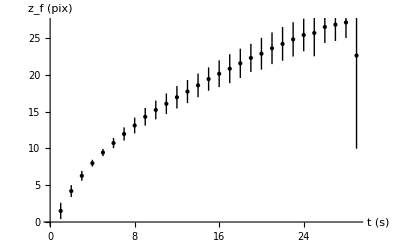
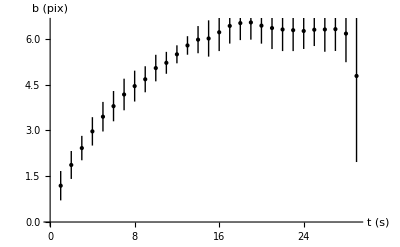
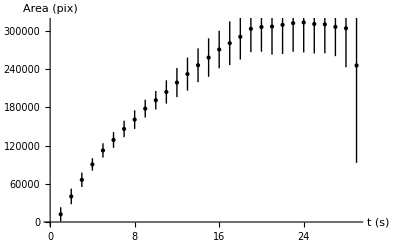
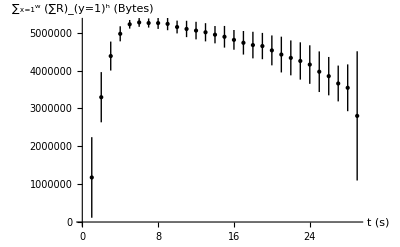
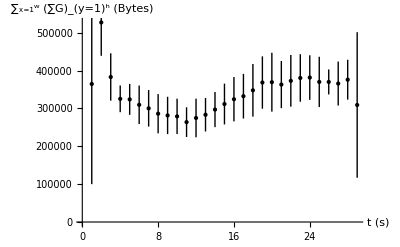
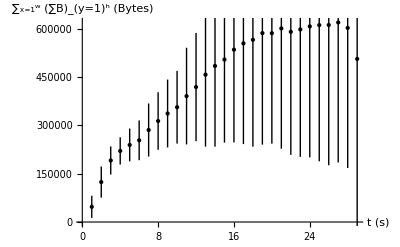
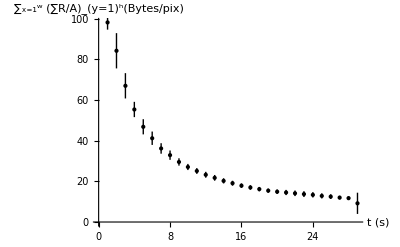
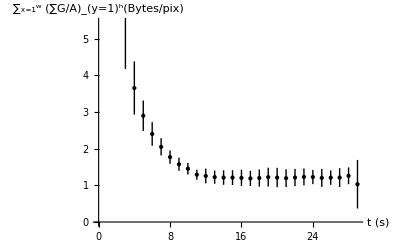

```mathematica
PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionMBI4, radiustMBI4, areaMBI4, redMBI4, greenMBI4, blueMBI4,cRedMBI4,cGreenMBI4,cBlueMBI4}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatacBlue,AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black]}
```

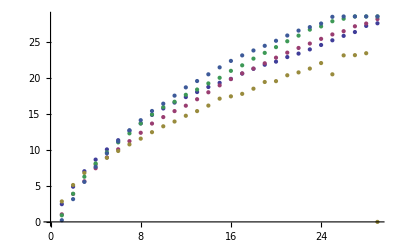
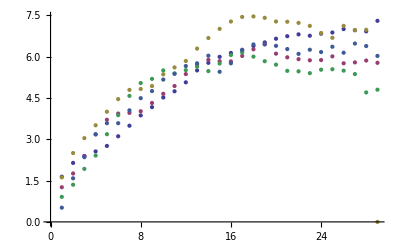
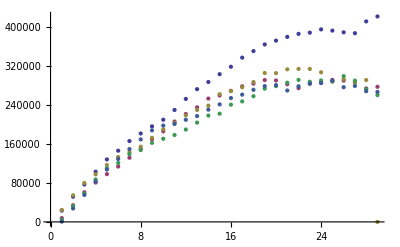
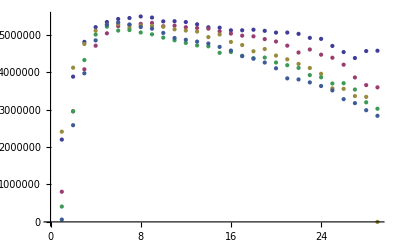
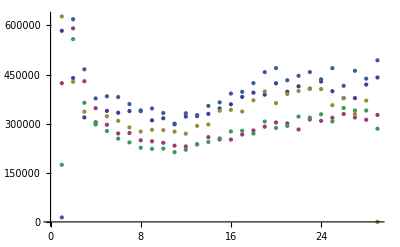
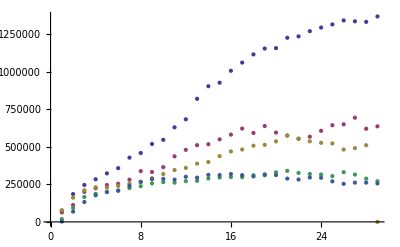
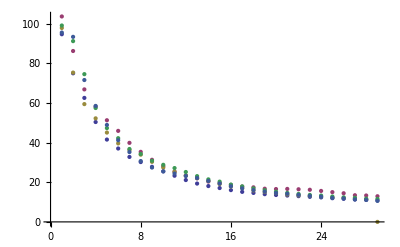
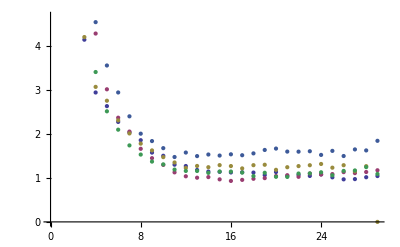

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

10^-4 M : Reactive

```mathematica
ntotal=5
```

5

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_4\MB_4_AscA~0.05M\

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_4\MB_4_AscA~0.05M\

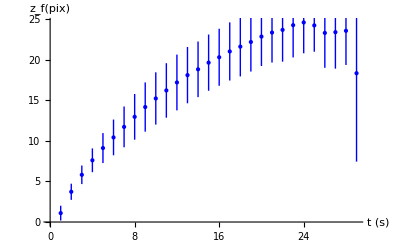
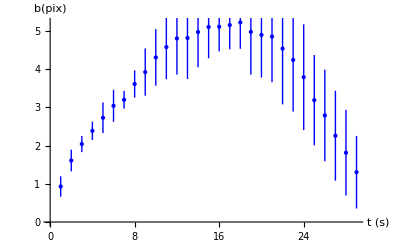
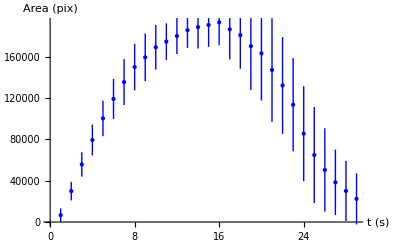
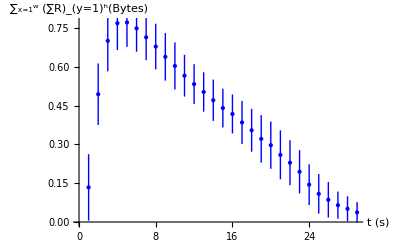
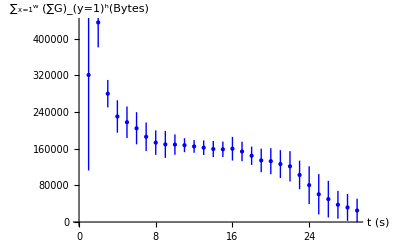
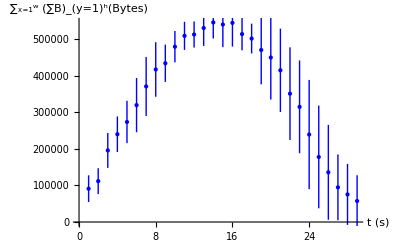
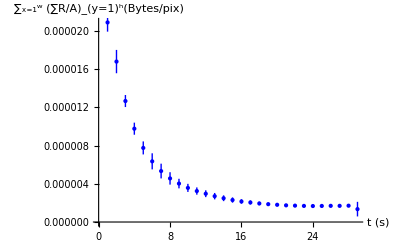
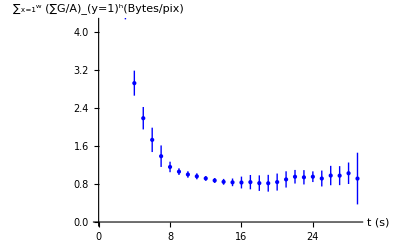

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_4\\MB_4_AscA~0.05M\\"
SetDirectory[dir1];
"C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_4\\MB_4_AscA~0.05M\\"
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGBRRminus4.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=(tRedAll0)^(-1)*m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};
Areac[n]=Area[n]/.{0.->10^8};

cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


(*If[n<4,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];*)

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];

mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]];

PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionMBR4, radiustMBR4, areaMBR4, redMBR4, greenMBR4, blueMBR4,cRedMBR4,cGreenMBR4,cBlueMBR4}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f(pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b(pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"}, PlotStyle->Blue],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->Blue],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->Blue],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Blue]}
```

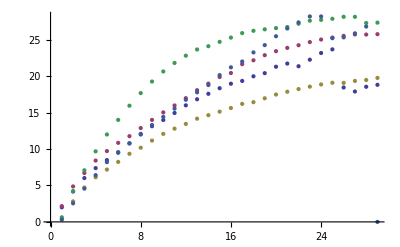
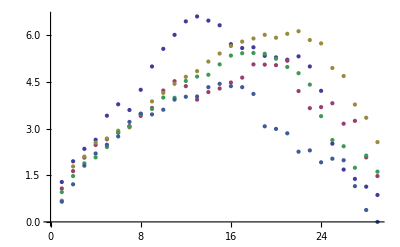
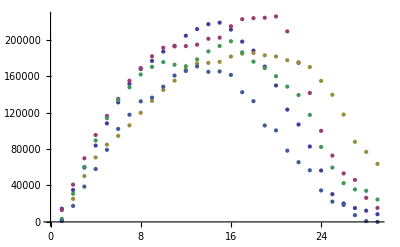
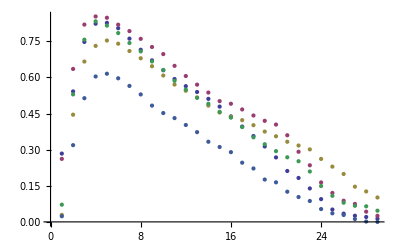
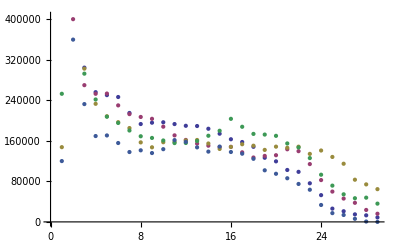
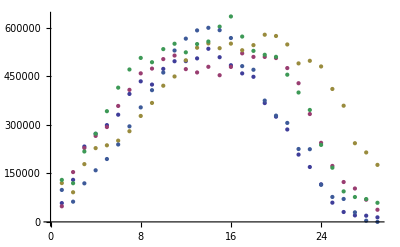
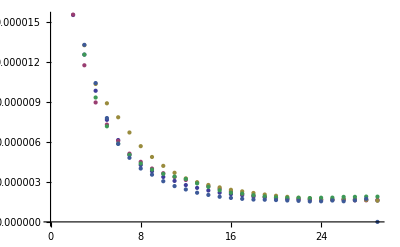
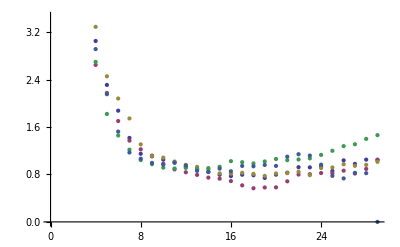

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

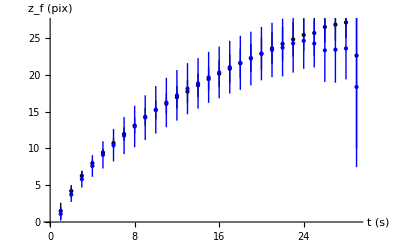

```mathematica
Show[{frontpositionMBI4,frontpositionMBR4},AxesOrigin->{0,0}]
```

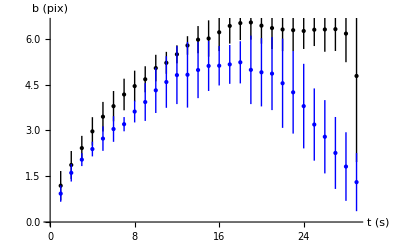

```mathematica
Show[{radiustMBI4,radiustMBR4},AxesOrigin->{0,0}]
```

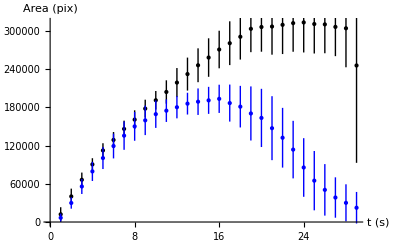

```mathematica
Show[{areaMBI4,areaMBR4},AxesOrigin->{0,0}]
```

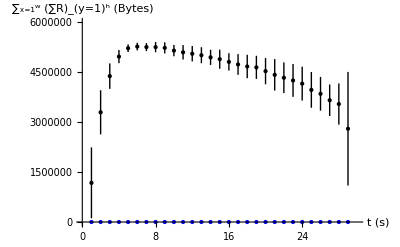

```mathematica
Show[{redMBI4,redMBR4},PlotRange->{{0,30},{0,6*10^6}},AxesOrigin->{0,0}]
```

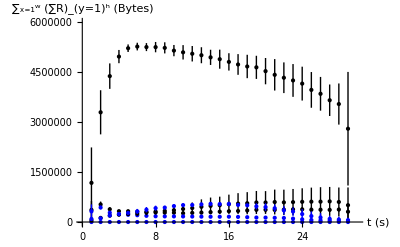

```mathematica
Show[ {redMBI4,redMBR4}, {greenMBI4,greenMBR4}, {blueMBI4,blueMBR4}, PlotRange->{{0,30},{0,6*10^6}}, AxesOrigin->{0,0}]
```

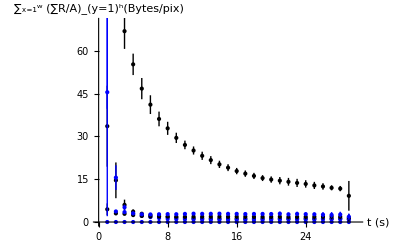

```mathematica
Show[ {cRedMBI4,cRedMBR4}, {cGreenMBI4,cGreenMBR4}, {cBlueMBI4,cBlueMBR4}, PlotRange->{{0,30},{0,70}}, AxesOrigin->{0,0}]
```

10^-3 M : Inert

```mathematica
ntotal=3
```

3

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_3\\MB_3_Inert\\"
SetDirectory[dir1];
```

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_3\MB_3_Inert\

```mathematica
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGBIminus3.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


(*If[n<4,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];*)

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];


mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

tRedAll0=Max[mtRedAll];
mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]]
```

{7.07034,4.814,2.47585,1.23935,0.439749,0.268585,0.378874,0.21629,0.205259,0.23348,0.169746,0.249756,0.276838,0.335679,0.460576,0.527041,0.545658,0.5339,0.665528,0.649858,0.670089,0.721046,0.683107,0.70028,0.730504,0.785702,0.761413,0.722716}

```mathematica
Needs["ErrorBarPlots`"]
```

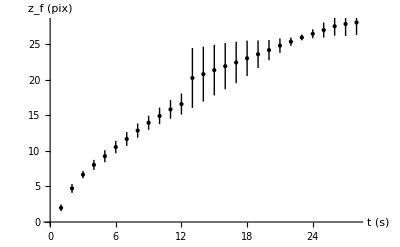
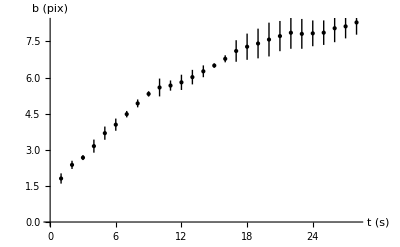
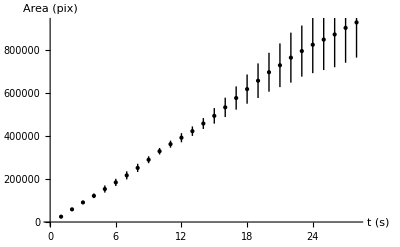
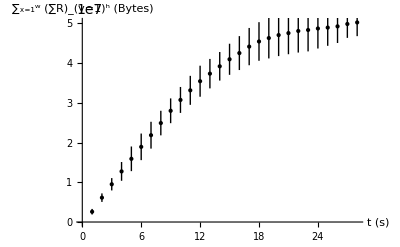
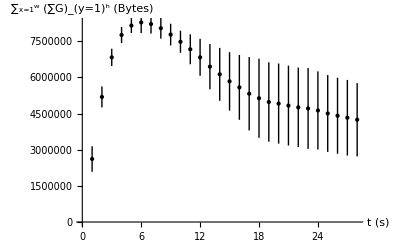
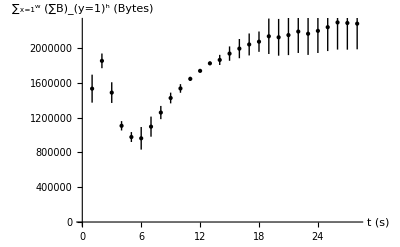
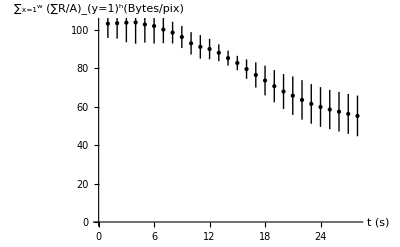
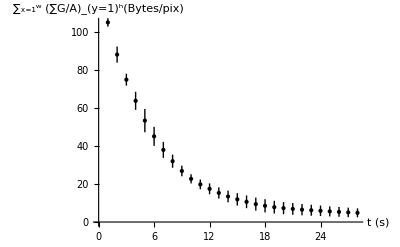

```mathematica
PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionMBI3, radiustMBI3, areaMBI3, redMBI3, greenMBI3, blueMBI3,cRedMBI3,cGreenMBI3,cBlueMBI3}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatacBlue,AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black]}
```

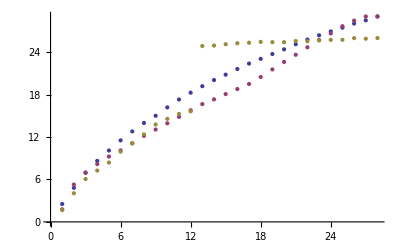
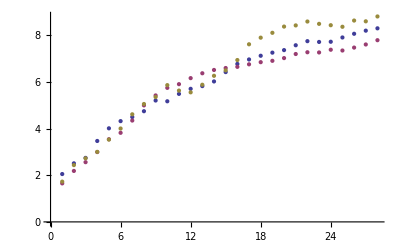
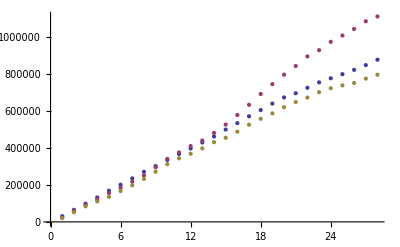
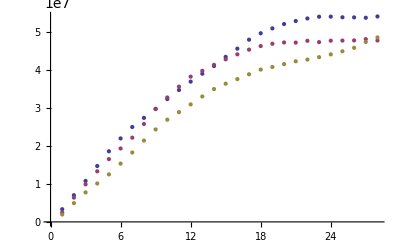
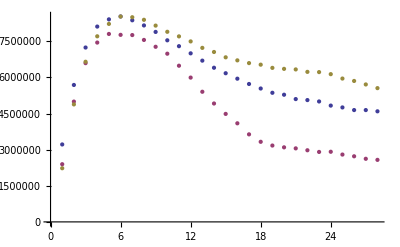
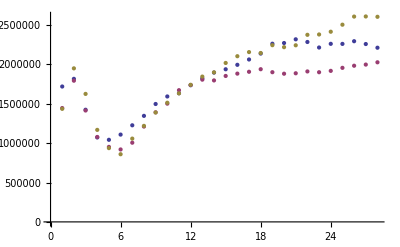
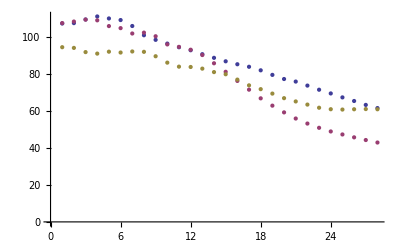
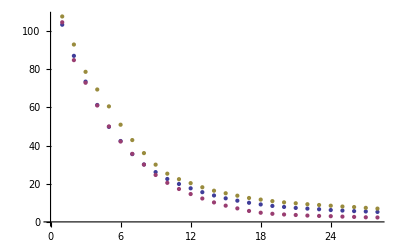

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

10^-3 M : Reactive

```mathematica
ntotal=7
```

7

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_3\MB_3_AscA~0.05M\

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_3\MB_3_AscA~0.05M\

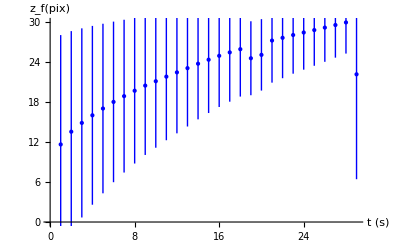
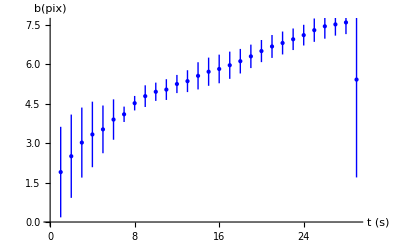
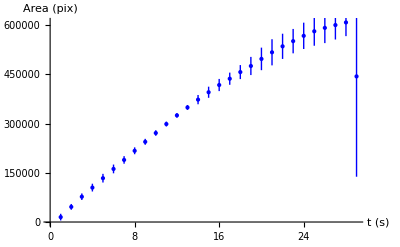
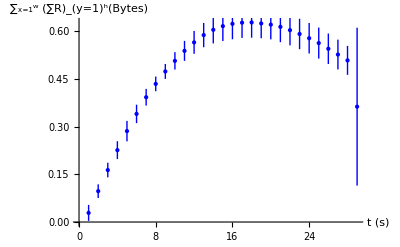
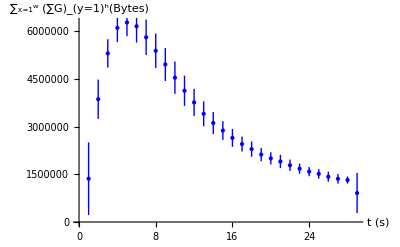
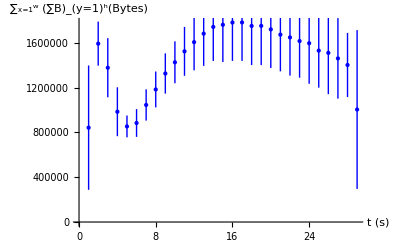
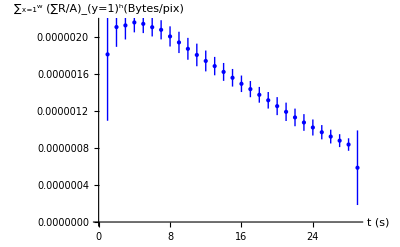
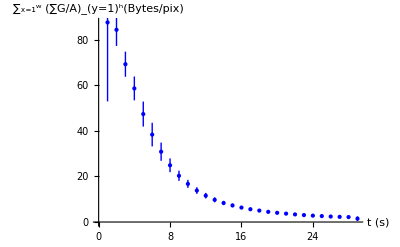

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_3\\MB_3_AscA~0.05M\\"
SetDirectory[dir1];
"C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_3\\MB_3_AscA~0.05M\\"
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGBRminus3.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=(tRedAll0)^(-1)*m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


If[n==2,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];

If[n==7,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];


mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]];

PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionMBR3, radiustMBR3, areaMBR3, redMBR3, greenMBR3, blueMBR3,cRedMBR3,cGreenMBR3,cBlueMBR3}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f(pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b(pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"}, PlotStyle->Blue],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->Blue],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->Blue],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Blue],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Blue]}
```

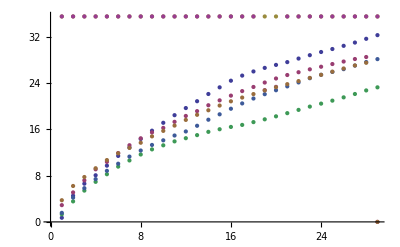
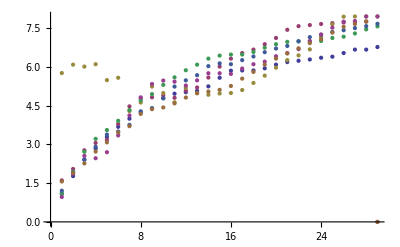
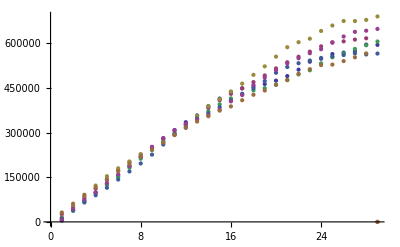
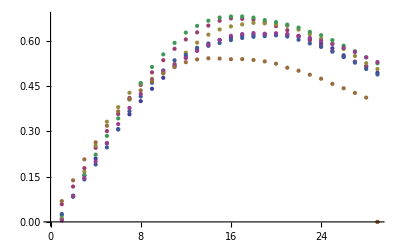
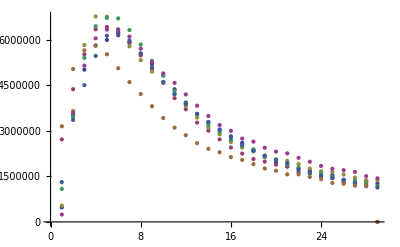
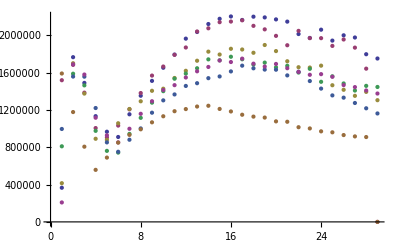
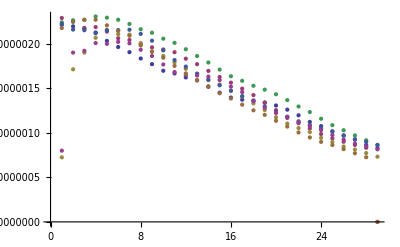
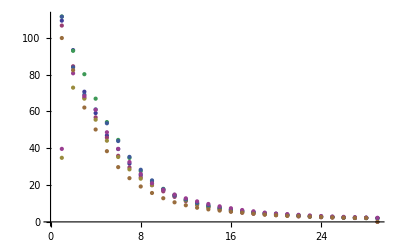

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

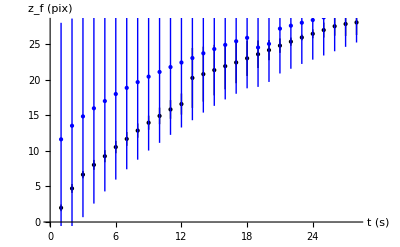

```mathematica
Show[{frontpositionMBI3,frontpositionMBR3},AxesOrigin->{0,0}]
```

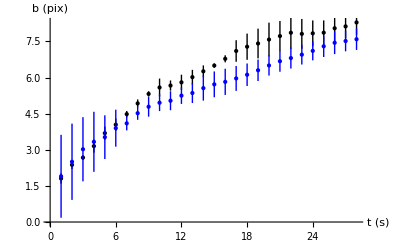

```mathematica
Show[{radiustMBI3,radiustMBR3},AxesOrigin->{0,0}]
```

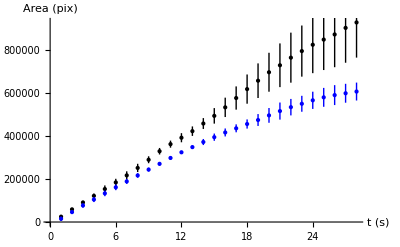

```mathematica
Show[{areaMBI3,areaMBR3},AxesOrigin->{0,0}]
```

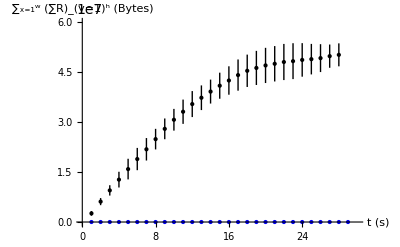

```mathematica
Show[{redMBI3,redMBR3},PlotRange->{{0,30},{0,6*10^7}},AxesOrigin->{0,0}]
```

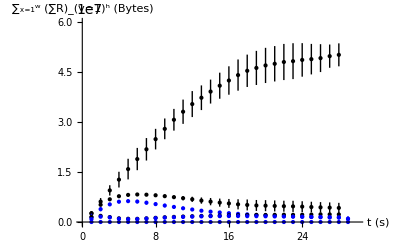

```mathematica
Show[ {redMBI3,redMBR3}, {greenMBI3,greenMBR3}, {blueMBI3,blueMBR3}, PlotRange->{{0,30},{0,6*10^7}}, AxesOrigin->{0,0}]
```

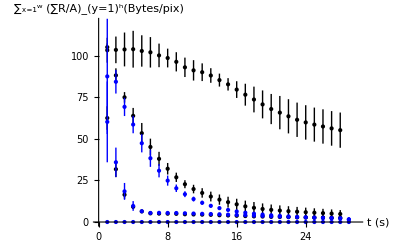

```mathematica
Show[ {cRedMBI3,cRedMBR3}, {cGreenMBI3,cGreenMBR3}, {cBlueMBI3,cBlueMBR3}, PlotRange->{{0,30},{0,120}}, AxesOrigin->{0,0}]
```

# Theory/Experiments : Ascorbic Acid - Methylene Blue System

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=10^(-4)*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=0
```

0

```mathematica
Grxn=0;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==lambda*m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=(na0)^(-1)*na[t]/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=lambda*vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

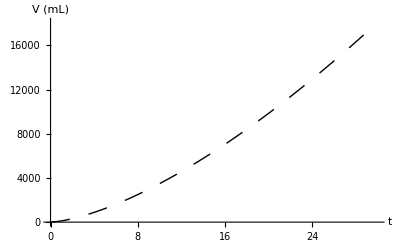
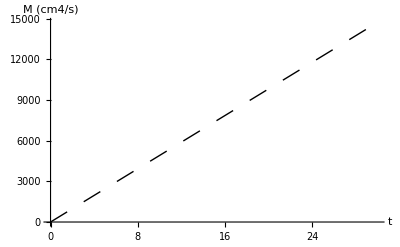
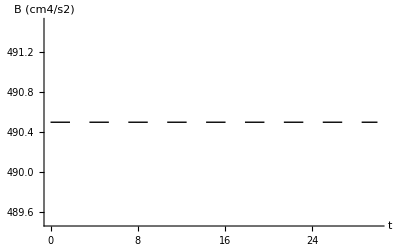
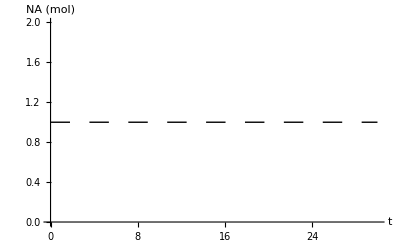
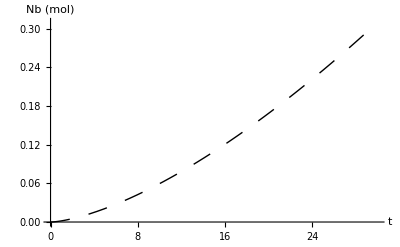
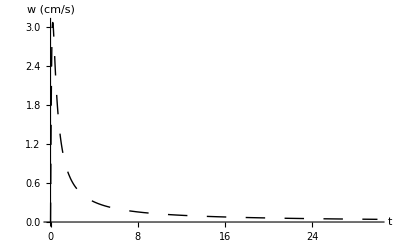
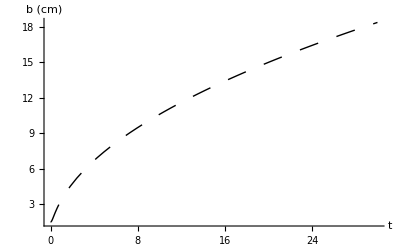
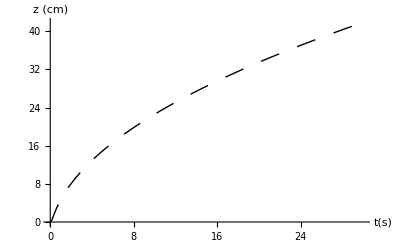

```mathematica
{g1I4,g2I4,g3I4,g4I4,g5I4,g6I4,g7I4,g8I4, g9I4, g10I4}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}]}
```

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {4.}. Try perturbing the initial point(s).

4.

```mathematica
zex[azero]
```

12.9141

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=10^(-4)*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=1*10^3;
```

```mathematica
Grxn=0;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==lambda*m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=(na0)^(-1)*na[t]/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=lambda*vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

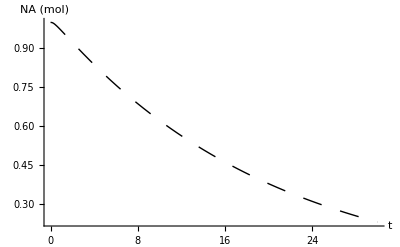
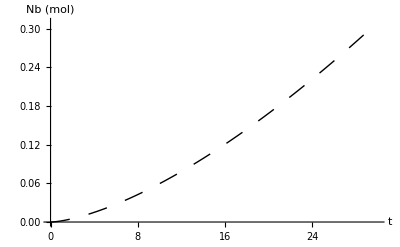
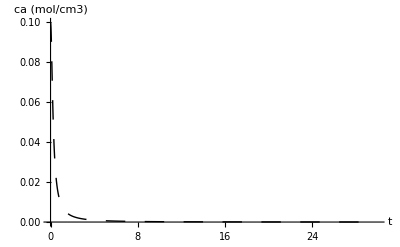
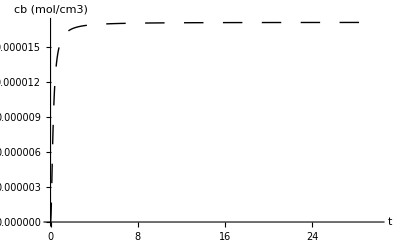
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{g1R4,g2R4,g3R4,g4R4,g5R4,g6R4,g7R4,g8R4, g9R4, g10R4}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}]}
```

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

InterpolatingFunction::dmval: Input value {44.2449} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.6443} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

61.246

```mathematica
zex[azero]
```

InterpolatingFunction::dmval: Input value {61.246} lies outside the range of data in the interpolating function. Extrapolation will be used.

62.8335

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=10^(-3)*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=0;
```

```mathematica
Grxn=0;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==lambda*m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=(na0)^(-1)*na[t]/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=lambda*vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

```mathematica
{g1I3,g2I3,g3I3,g4I3,g5I3,g6I3,g7I3,g8I3, g9I3, g10I3}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {4.}. Try perturbing the initial point(s).

4.

```mathematica
zex[azero]
```

12.9141

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=10^(-3)*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=1*10^3;
```

```mathematica
Grxn=0;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=14
```

14

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==lambda*m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,14.}},<>],m→InterpolatingFunction[{{0.0001,14.}},<>],b→InterpolatingFunction[{{0.0001,14.}},<>],na→InterpolatingFunction[{{0.0001,14.}},<>],nb→InterpolatingFunction[{{0.0001,14.}},<>],height→InterpolatingFunction[{{0.0001,14.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=(na0)^(-1)*na[t]/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=lambda*vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

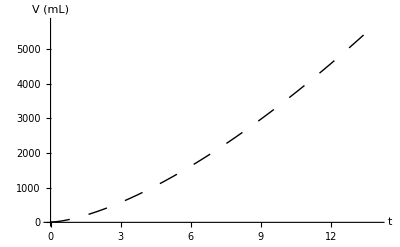
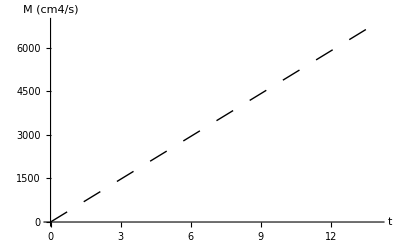
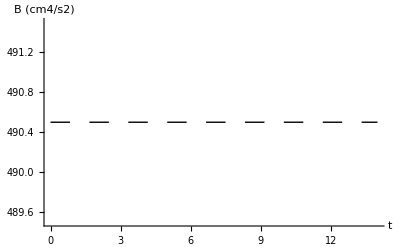
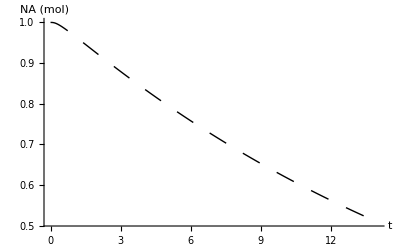
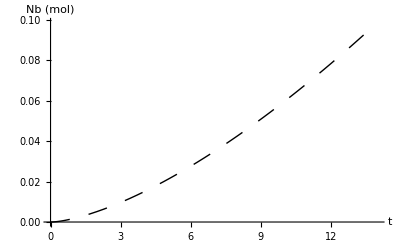
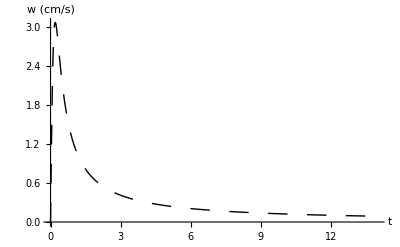
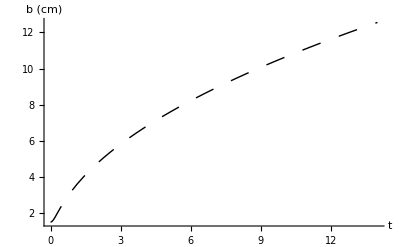
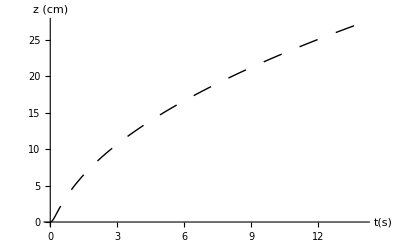

```mathematica
{g1R3,g2R3,g3R3,g4R3,g5R3,g6R3,g7R3,g8R3, g9R3, g10R3}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}]}
```

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,13}]
```

InterpolatingFunction::dmval: Input value {33.0399} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47.408} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

46.0751

```mathematica
zex[azero]
```

InterpolatingFunction::dmval: Input value {46.0751} lies outside the range of data in the interpolating function. Extrapolation will be used.

67.3378

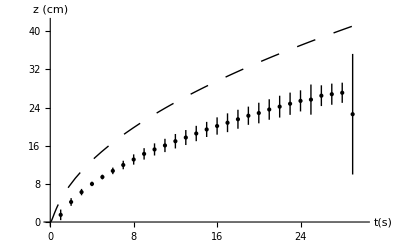
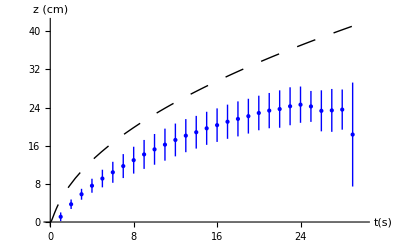
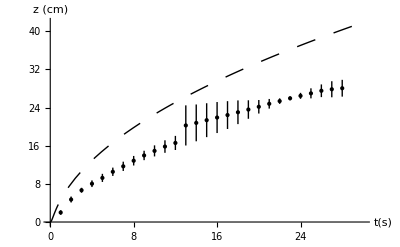
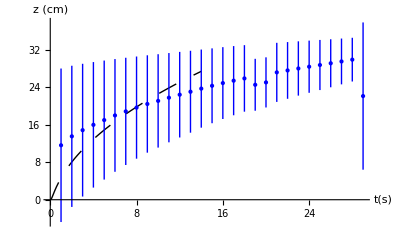

```mathematica
{Joinfp1,Joinfp2,Joinfp3,Joinfp4}={Show[g8I4,frontpositionMBI4],Show[g8R4,frontpositionMBR4],Show[g8I3,frontpositionMBI3],Show[g8R3,frontpositionMBR3]}
```

```mathematica
{Joinradius1,Joinradius2,Joinradius3,Joinradius4}={Show[g7I4,radiustMBI4],Show[g7R4,radiustMBR4],Show[g7I3,radiustMBI3],Show[g7R3,radiustMBR3]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Joinna4,Joinna3}={Show[g4R4,redMBR4],Show[g4R3,redMBR3]}
```

{-Graphics-,-Graphics-}